```mathematica
T:={{1},{ x}}
Do[T=Append[T,Expand[2*x*T[[i]]-T[[i-1]]]],{i,2,6}]
T=Flatten[T]
```

{1,x,-1+2 x^2,-3 x+4 x^3,1-8 x^2+8 x^4,5 x-20 x^3+16 x^5,-1+18 x^2-48 x^4+32 x^6}

```mathematica
P=Evaluate[Normal[Table[Series[x*Exp[x],{x,0,i}],{i,1,6}]]]
```

{x,x+x^2,x+x^2+x^3/2,x+x^2+x^3/2+x^4/6,x+x^2+x^3/2+x^4/6+x^5/24,x+x^2+x^3/2+x^4/6+x^5/24+x^6/120}

```mathematica
P[[6]]
T[[6+1]]
```

x+x^2+x^3/2+x^4/6+x^5/24+x^6/120

-1+18 x^2-48 x^4+32 x^6

```mathematica
P5[x_]:=P[[6]]-(1/120)*(1/2^(6-1))*T[[6+1]]//Expand
P5[x]
P4[x_]:=P[[5]]-(1/24)*(1/2^(5-1))*T[[5+1]]//Expand
P4[x]
P3[x_]:=P[[4]]-(1/6)*(1/2^(4-1))*T[[4+1]]//Expand
P3[x]
P2[x_]:=P[[3]]-(1/2)*(1/2^(3-1))*T[[3+1]]//Expand
P2[x]
```

1/3840+x+(637 x^2)/640+x^3/2+(43 x^4)/240+x^5/24

(379 x)/384+x^2+(53 x^3)/96+x^4/6

-1/48+x+(7 x^2)/6+x^3/2

(11 x)/8+x^2

```mathematica
P5[x]
P4b[x_]:=P5[x]-(1/24)*(1/2^(5-1))*T[[5+1]]//Expand
P4b[x]
P3b[x_]:=P4b[x]-(43/240)*(1/2^(4-1))*T[[4+1]]//Expand
P3b[x]
P2b[x_]:=P3b[x]-(53/96)*(1/2^(3-1))*T[[3+1]]//Expand
P2b[x]
```

1/3840+x+(637 x^2)/640+x^3/2+(43 x^4)/240+x^5/24

1/3840+(379 x)/384+(637 x^2)/640+(53 x^3)/96+(43 x^4)/240

-17/768+(379 x)/384+(451 x^2)/384+(53 x^3)/96

-17/768+(269 x)/192+(451 x^2)/384

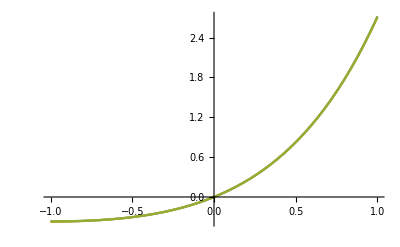

```mathematica
Plot[{x*Exp[x],P[[5]], P5[x]},{x,-1,1}]
```

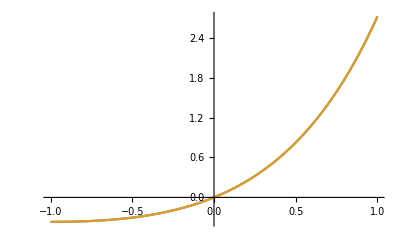

```mathematica
Plot[{x*Exp[x],P5[x]},{x,-1,1}]
```

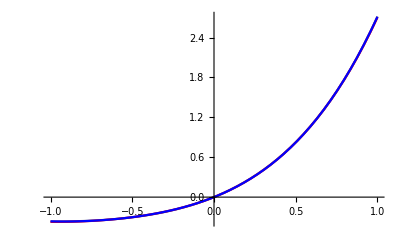

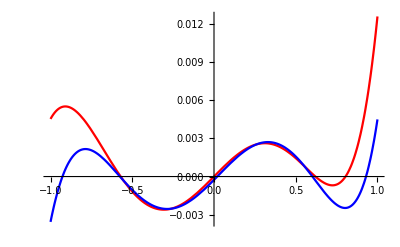

```mathematica
Plot[{x*Exp[x],P4[x], P4b[x]},{x,-1,1}, PlotStyle->{Gray, Red, Blue}]
Plot[{x*Exp[x]-P4[x],x*Exp[x]- P4b[x]},{x,-1,1}, PlotStyle->{Red, Blue}]
```

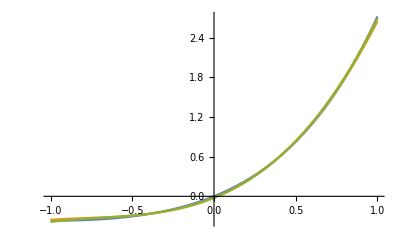

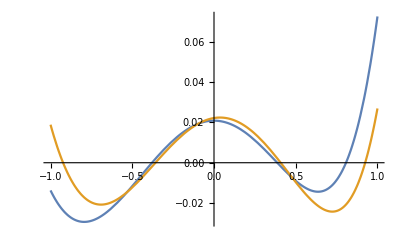

```mathematica
Plot[{x*Exp[x],P3[x], P3b[x]},{x,-1,1}]
Plot[{x*Exp[x]-P3[x],x*Exp[x]- P3b[x]},{x,-1,1}]
```

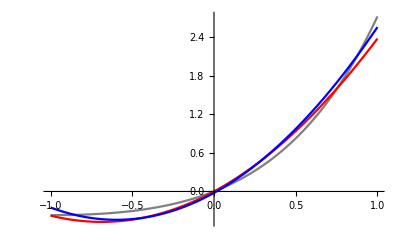

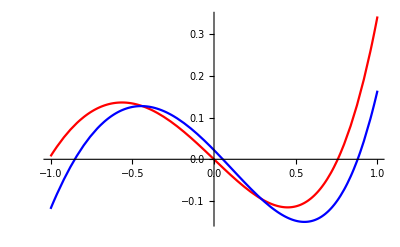

```mathematica
Plot[{x*Exp[x],P2[x], P2b[x]},{x,-1,1}, PlotStyle->{Gray, Red, Blue}]
Plot[{x*Exp[x]-P2[x],x*Exp[x]- P2b[x]},{x,-1,1}, PlotStyle->{ Red, Blue}]
```

```mathematica
f[x_]:=x*Exp[x]
```

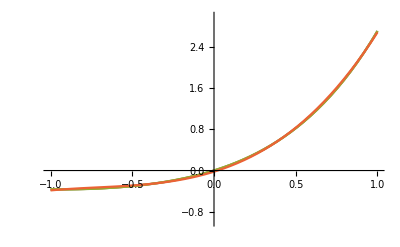

```mathematica
Plot[{f[x],P5[x],P4b[x],P3b[x]},{x,-1,1},PlotRange->{-1,3}]
```

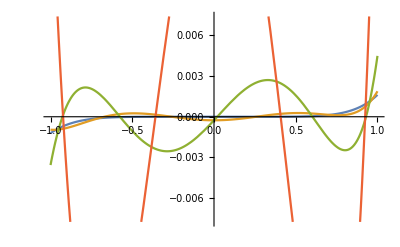

```mathematica
Plot[{f[x]-P[[6]],f[x]-P5[x],f[x]-P4b[x],f[x]-P3b[x]},{x,-1,1}]
```